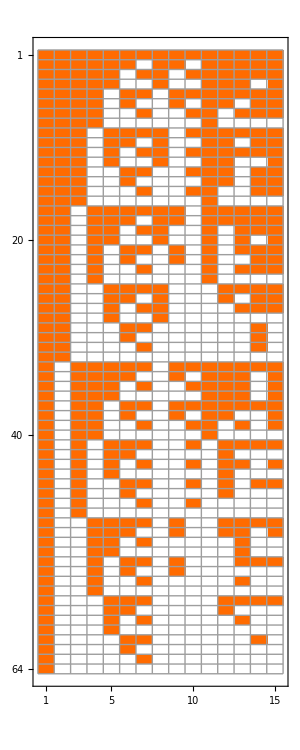
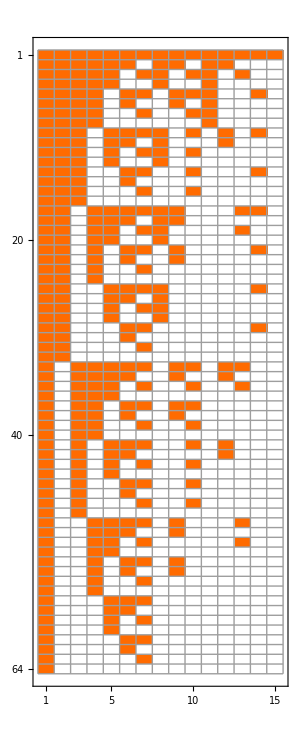

```mathematica
Row[{
MatrixPlot[Sort[Table[VectorOne[BaseCoeff4[k,"E"]],{k,Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&]}],FromDigits[#1,2]>FromDigits[#2,2]&],Mesh->All,ImageSize->300],
MatrixPlot[Sort[Table[BaseCoeff4[k,"C"],{k,Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&]}],FromDigits[#1,2]>FromDigits[#2,2]&],Mesh->All,ImageSize->300]
},ImageSize->1200]
```

```mathematica
Sort[Table[Total[BaseCoeff4[k,"C"]],{k,Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&]}]]//Tally
```

{{1,1},{2,6},{3,12},{4,7},{5,16},{7,15},{10,6},{15,1}}

```mathematica
VectorSize[vect_]:=Total[Map[If[#==0,0,1]&,vect]]
```

```mathematica
Vector1[vect_]:=Map[If[#==0,0,1]&,vect]
```

```mathematica
Rest[Total[Table[Vector1[BaseCoeff4[k,"G"]],{k,Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&]}]]]//Total
```

170

```mathematica
Total[Table[Vector1[BaseCoeff4[k,"C"]],{k,Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&]}]]//Total
```

337

```mathematica
Total[Table[Vector1[BaseCoeff4[k,"E"]],{k,Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&]}]]//Total
```

470

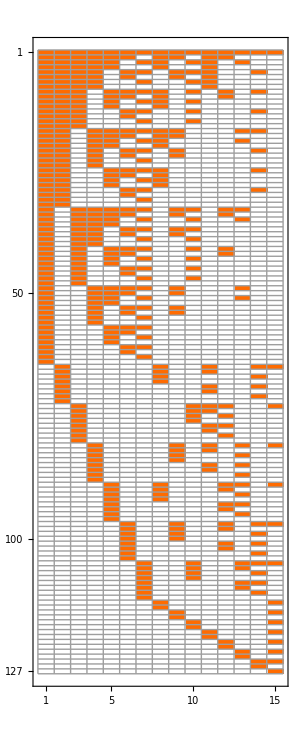

```mathematica
MatrixPlot[Sort[Table[BaseCoeff4[k,"C"],{k,Keys[allGraphs4]}],FromDigits[#1,2]>FromDigits[#2,2]&],Mesh->All,ImageSize->300]
```

```mathematica
With[
{base="C"},
Map[Style[#,Red,20]&,((Sort[Table[VectorOne[BaseCoeff4[k,base]],{k,Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&]}],FromDigits[#1,2]>FromDigits[#2,2]&]//Total))]*(Map[Labeled[ShowGraph[allGraphs4,#],allGraphs4[#,Bases4[base,"Colofour"]]]&, Bases4[base,"AtomKeys"]])
]
```

{-Graphics-364v1x2x3x4 64,-Graphics-365v1x2x34 32,-Graphics-373v1x23x4 32,-Graphics-367v1x24x3 32,-Graphics-607v12x3x4 32,-Graphics-445v13x2x4 32,-Graphics-391v14x2x3 32,-Graphics-608v12x34 16,-Graphics-448v13x24 16,-Graphics-400v14x23 16,-Graphics-377v1x234 8,-Graphics-697v123x4 8,-Graphics-637v124x3 8,-Graphics-473v134x2 8,-Graphics-728v1234 1}

```mathematica
Bases4["G","Colofour"]
```

colofourgenerator

```mathematica
With[
{base="G"},
Map[Style[#,Red,20]&,((Sort[Table[VectorOne[BaseCoeff4[k,base]],{k,Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&]}],FromDigits[#1,2]>FromDigits[#2,2]&]//Total))]*(Map[Labeled[ShowGraph[allGraphs4,#],allGraphs4[#,Bases4[base,"Colofour"]]]&, Bases4[base,"AtomKeys"]])
]
```

{-Graphics-364g1x2x3x4 38,-Graphics-363g1x2x34 16,-Graphics-355g1x23x4 16,-Graphics-361g1x24x3 16,-Graphics-121g12x3x4 16,-Graphics-283g13x2x4 16,-Graphics-337g14x2x3 16,-Graphics-120g12x34 15,-Graphics-280g13x24 15,-Graphics-328g14x23 15,-Graphics-351g1x234 7,-Graphics-31g123x4 7,-Graphics-91g124x3 7,-Graphics-255g134x2 7,-Graphics-0g1234 1}

```mathematica
With[
{base="E"},
Map[Style[#,Red,20]&,((Sort[Table[VectorOne[BaseCoeff4[k,base]],{k,Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&]}],FromDigits[#1,2]>FromDigits[#2,2]&]//Total))]*(Map[Labeled[ShowGraph[allGraphs4,#],allGraphs4[#,Bases4[base,"Colofour"]]]&, Bases4[base,"AtomKeys"]])
]
```

{-Graphics-0n1x2x3x4 64,-Graphics-2n1x2x34 32,-Graphics-18n1x23x4 32,-Graphics-6n1x24x3 32,-Graphics-486n12x3x4 32,-Graphics-162n13x2x4 32,-Graphics-54n14x2x3 32,-Graphics-488n12x34 16,-Graphics-168n13x24 16,-Graphics-72n14x23 16,-Graphics-26n1x234 32,-Graphics-666n123x4 32,-Graphics-546n124x3 32,-Graphics-218n134x2 32,-Graphics-728n1234 38}

```mathematica
Map[ShowGraph[allGraphs4,#]&,Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&&!MemberQ[ListofVars[allGraphs4[#,"colofourrealnull"]],n1234]&]]
```

{-Graphics-0,-Graphics-243,-Graphics-324,-Graphics-333,-Graphics-270,-Graphics-273,-Graphics-252,-Graphics-246,-Graphics-244,-Graphics-81,-Graphics-108,-Graphics-109,-Graphics-90,-Graphics-84,-Graphics-82,-Graphics-27,-Graphics-36,-Graphics-30,-Graphics-28,-Graphics-9,-Graphics-12,-Graphics-13,-Graphics-10,-Graphics-3,-Graphics-4,-Graphics-1}

```mathematica
Map[ShowGraph[allGraphs4,#]&,Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&&!MemberQ[ListofVars[allGraphs4[#,"colofourgenerator"]],g1x2x3x4]&]]
```

{-Graphics-0,-Graphics-324,-Graphics-351,-Graphics-363,-Graphics-361,-Graphics-355,-Graphics-337,-Graphics-328,-Graphics-270,-Graphics-283,-Graphics-280,-Graphics-252,-Graphics-255,-Graphics-246,-Graphics-108,-Graphics-120,-Graphics-121,-Graphics-90,-Graphics-91,-Graphics-82,-Graphics-30,-Graphics-31,-Graphics-28,-Graphics-12,-Graphics-10,-Graphics-4}

```mathematica
Map[ShowGraph[allGraphs4,#]&,Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&&MemberQ[ListofVars[allGraphs4[#,"colofourgenerator"]],g1x2x3x4]&]]
```

{-Graphics-243,-Graphics-360,-Graphics-364,-Graphics-354,-Graphics-352,-Graphics-333,-Graphics-336,-Graphics-334,-Graphics-327,-Graphics-325,-Graphics-279,-Graphics-282,-Graphics-273,-Graphics-274,-Graphics-271,-Graphics-256,-Graphics-253,-Graphics-247,-Graphics-244,-Graphics-81,-Graphics-117,-Graphics-118,-Graphics-111,-Graphics-112,-Graphics-109,-Graphics-93,-Graphics-94,-Graphics-84,-Graphics-85,-Graphics-27,-Graphics-36,-Graphics-39,-Graphics-40,-Graphics-37,-Graphics-9,-Graphics-13,-Graphics-3,-Graphics-1}

```mathematica
VectorOne[vect_]:=Map[If[#==0,0,1]&,vect]
```

```mathematica
((Sort[Table[VectorOne[BaseCoeff4[k,"E"]],{k,Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&]}],FromDigits[#1,2]>FromDigits[#2,2]&]//Total)/64)*(Map[allGraphs4[#,"graph"]&, Bases4["E","AtomKeys"]])
```

{-Graphics-,(-Graphics-)/2,(-Graphics-)/2,(-Graphics-)/2,(-Graphics-)/2,(-Graphics-)/2,(-Graphics-)/2,(-Graphics-)/4,(-Graphics-)/4,(-Graphics-)/4,(-Graphics-)/2,(-Graphics-)/2,(-Graphics-)/2,(-Graphics-)/2,(19 -Graphics-)/32}

```mathematica
Sort[Table[VectorOne[BaseCoeff4[k,"E"]],{k,Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&]}],FromDigits[#1,2]>FromDigits[#2,2]&]==Sort[Table[VectorOne[BaseCoeff4[k,"C"]],{k,Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&]}],FromDigits[#1,2]>FromDigits[#2,2]&]
```

False